```mathematica
(*проверка принадлежит ли точка массиву или  нет*)
IsDistinctQ[P_,q_]:=Block[
{flag=True,i},
For[i=1,i≤Length[P],i++,{
If[q==P⟦i⟧,flag=False;Break[]
]}];
Return[flag];
]
(*создания массива точек*)
CreatePoints[Size_]:=Block[
{K={},q,n=50,i},
For[i=1,i≤Size,i++,{
q={RandomInteger[{-n,n}],RandomInteger[{-n,n}]};
If[IsDistinctQ[K,q],AppendTo[K,q],i--]; (*проверка существует ли точка в массиве или нет*)
}];
Return[K];(*возвращается массив точек*)
]
(*расположение точек*)
IsLeftQ[p1_,p2_,p3_]:=Block[
{flag=True},
If[Det[{p2-p1,p3-p1}]≥0,flag=True,flag=False];
Return[flag];
]
```

```mathematica
(*если угол между ветором (p[i], нижняя точка) меньше чем "минимальный"(начиная с 2 π) угол и p[i] не первая точка (те не нулевой вектор) меняем значение минимального угла и присваиваем концу начальной линии значение p[i]. Те ищем самый прижатый к Ох вектор *)
```

```mathematica
FindStartLine[P_]:=Block[
{first,second,i,minAngle=2π},
first=FindMostDownPoint[P];
For[i=1,i≤Length[P],i++,{
If[VectorAngle[P⟦i⟧-first,{1,0}]<minAngle&&P⟦i⟧≠first,{ 
minAngle=VectorAngle[P⟦i⟧-first,{1,0}];
second=P⟦i⟧}]
}];
Return[{first,second}]
]
(*поиск нижней точки*)
(* сравниваем заданную с i-той, возвращаем дальнюю*)
FindMostDownPoint[P_]:=Block[
{i,mostDown=P⟦1⟧},
For[i=2,i≤Length[P],i++,{
If[mostDown⟦2⟧>P⟦i⟧⟦2⟧,mostDown=P⟦i⟧]
}];
Return[mostDown]
]
(*Нахождение самого большого угла*)
(*Если угол между ветором(q1-p[i], q2-p[i]) больлше чем заданный уже угол и p[i] лежит левее начальной прямой  меняем значение максимального угла и присваиваем res эту точку. Возращаем точку *)
FindMostBigAngle[P_,q1_,q2_]:=Block[
{i,angle=0,res={}},
For[i=1,i≤Length[P],i++,{
If[VectorAngle[q1-P⟦i⟧,q2-P⟦i⟧]>angle&&IsLeftQ[q1,q2,P⟦i⟧],
angle=VectorAngle[q1-P⟦i⟧,q2-P⟦i⟧];res=P⟦i⟧]
}];
Return[res]
]
(*новая триангуляция*)
(*если полученный массив triangulation отсортированный по возрастанию х совпадает strian, то возвращаем false. Иначе возращаем true, те это новая триангуляция *)
IsNewTriangular[Trian_]:=Block[
{i,flag=True,STrian=Sort[Trian,#1⟦1⟧<#2⟦1⟧&] (*сортируем значаения массива trian по возрастанию х*)},
For[i=1,i≤Length[Triangulation],i++,{
If[Sort[Triangulation⟦i⟧,#1⟦1⟧<#2⟦1⟧&]==STrian,flag=False;Break[]]
}];
Return[flag]
]
(*Создание триангуляции (массив точек и 2 точки, составляющие "начальную" линию)*)
CreateTriangulation[P_,q1_,q2_]:=Block[
{newPoint,i},
newPoint=FindMostBigAngle[P,q1,q2]; (*находим точку с которой "начальная" линия образует самый большой угол*) 
If[Length[newPoint]==0,Return[],{
If[IsNewTriangular[{q1,newPoint,q2}],{
(*если тру добавляем эти точки в массив Triangulation*)
AppendTo[Triangulation,{q1,newPoint,q2}];
(*рекурсивно создаем триангуляцию с новой начальной прямой до тех пор пока будет находится новая точка с которой начальные прямые образуют максимальны угол*)
CreateTriangulation[P,q1,newPoint];
CreateTriangulation[P,newPoint,q2];
}]
}];
]
```

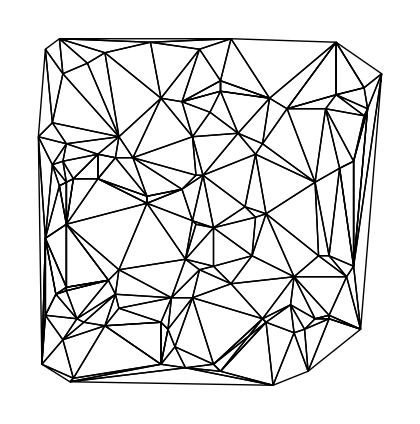

```mathematica
Triangulation={};
P=CreatePoints[100];
startLine=FindStartLine[P];
CreateTriangulation[P,startLine⟦1⟧,startLine⟦2⟧]; 

Graphics[{
Table[Line[Append[Triangulation⟦i⟧,Triangulation⟦i⟧⟦1⟧]],{i,1,Length[Triangulation]}]
}]
```